```mathematica
(*Проверка на совпадение*)
```

```mathematica
IsDistinct[P_,q_]:=Block[
{flag=True,i},
For[i=1,i≤Length[P],i++,{
If[q==P⟦i⟧,flag=False;Break[]
]}];
Return[flag];
]
(*Создание массива точек*)
CreatePoints[Size_]:=Block[
{K={},q,rang=50,i},
For[i=1,i≤Size,i++,{
q={RandomInteger[{-rang,rang}],RandomInteger[{-rang,rang}]};
If[IsDistinct[K,q],AppendTo[K,q],i--];
}];
Return[K];
]
(*Проверка на положение относительно прямой*)
IsLeftPos[p1_,p2_,p3_]:=Block[
{flag=True},
If[Det[{p2-p1,p3-p1}]≥0,flag=True,flag=False];
Return[flag];
]
```

```mathematica
(*Нахожение стартовой линии*)
```

```mathematica
FindStartLine[P_]:=Block[
{first,second,i,minAngle=2π},
first=FindMostDownPoint[P];(*1-ая точка - самая минимальная по координате Y точка*)
For[i=1,i≤Length[P],i++,{
If[VectorAngle[P⟦i⟧-first,{1,0}]<minAngle&&P⟦i⟧≠first,{
minAngle=VectorAngle[P⟦i⟧-first,{1,0}];
second=P⟦i⟧}]
}];
Return[{first,second}](*возращаем точку с минимальным Y и точку со вторым по величине Y. Их соединени и будет стартовой линией*)
]
(*Нахождение точки с минимальным Y*)
FindMostDownPoint[P_]:=Block[
{i,mostDown=P⟦1⟧},
For[i=2,i≤Length[P],i++,{
If[mostDown⟦2⟧>P⟦i⟧⟦2⟧,mostDown=P⟦i⟧](*если Y самой нижней точки больше Y текущей точки, то присваиваем значение самой нижней точки - текущей*)
}];
Return[mostDown]
]
(*Нахождение точки с наибольшим углом, образующим треугольник*)
FindMostBigAngle[P_,q1_,q2_]:=Block[
{i,angle=0,res={}},
For[i=1,i≤Length[P],i++,{
If[VectorAngle[q1-P⟦i⟧,q2-P⟦i⟧]>angle&&IsLeftPos[q1,q2,P⟦i⟧],
angle=VectorAngle[q1-P⟦i⟧,q2-P⟦i⟧];res=P⟦i⟧]
}];
Return[res]
]
(*Проверка на создание нового треугольника*)
IsNewTriangular[Triangle_]:=Block[
{i,flag=True,Triang=Sort[Triangle,#1⟦1⟧<#2⟦1⟧&]},
For[i=1,i≤Length[Triangulation],i++,{
If[Sort[Triangulation⟦i⟧,#1⟦1⟧<#2⟦1⟧&]==Triang,flag=False;Break[]]
}];
Return[flag]
]
(*Рекурсивное создание триангуляции*)
CreateTriangulation[P_,q1_,q2_]:=Block[
{newPoint,i},
newPoint=FindMostBigAngle[P,q1,q2];
If[Length[newPoint]==0,Return[],{
If[IsNewTriangular[{q1,newPoint,q2}],{
AppendTo[Triangulation,{q1,newPoint,q2}];
CreateTriangulation[P,q1,newPoint];
CreateTriangulation[P,newPoint,q2];
}]
}];
]
```

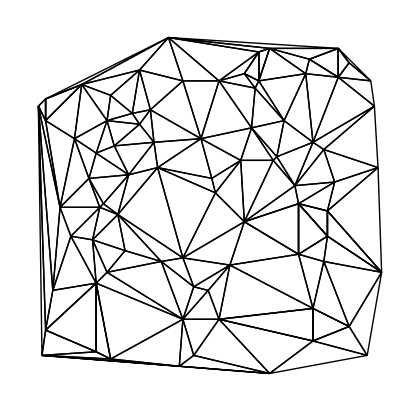

```mathematica
Triangulation={};
P=CreatePoints[80];
startLine=FindStartLine[P];
CreateTriangulation[P,startLine⟦1⟧,startLine⟦2⟧];
Graphics[{
Table[Line[Append[Triangulation⟦i⟧,Triangulation⟦i⟧⟦1⟧]],{i,1,Length[Triangulation]}]
}]
```